Photodiode noise, mostly based on the Rev. Sci. Inst. 76, 113101 (2005) paper by Bickman and DeMille

First, a constant which gives Johnson noise in nV/√Hz when multiplied by √R[Ω].

```mathematica
jonNoise = 12.7;
```

```mathematica
magnitude[x_]:= √ComplexExpand[(x/.s-> ⅈ 2 π f)(x/.s-> -ⅈ 2 π f)]//Simplify
```

We follow the circuit of figure 1 of the paper, but mostly drop Rs because it is very small compared to the other resistances.

```mathematica
enout= (1+(rf/(1+s cf rf))/(rj/(1+s ci rj))) en
```

en (1+(rf (1+ci rj s))/(rj (1+cf rf s)))

```mathematica
enf= magnitude[enout]
```

√((en^2 (2 rf rj+rj^2+rf^2 (1+4 cf^2 f^2 π^2 rj^2+8 cf ci f^2 π^2 rj^2+4 ci^2 f^2 π^2 rj^2)))/((1+4 cf^2 f^2 π^2 rf^2) rj^2))

```mathematica
myCircuit = {rf->3.3 10^5, cf -> 4.7 10^-11, ci ->8.5 10^-11, rj-> 1 10^9,  en-> 30};
```

```mathematica
enoutn = enf/.myCircuit;
```

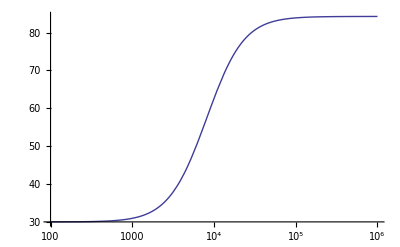

```mathematica
LogLinearPlot[enoutn,{f,100,10^6},PlotRange->All]
```

```mathematica
gain = rf/(1+s cf rf);
```

```mathematica
gainf=magnitude[gain]
```

√(rf^2/(1+4 cf^2 f^2 π^2 rf^2))

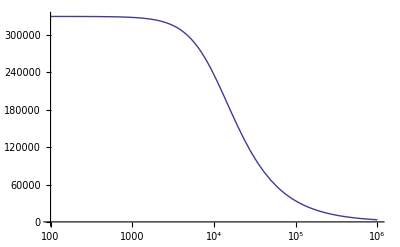

```mathematica
LogLinearPlot[gainf/.myCircuit,{f,100,10^6}]
```